# Calculation of eikonal corrections at KE = 50 MeV

9/17/13

## Define Constants

```mathematica
mp=0.938272046;(*GeV/c^2*)
mn=1.00137842*mp(*GeV/c^2*);
M=2*mp+2*mn;
m=M/4;
ℏc=0.19732697178(*Giga ElectronVolt*Femto Meter*);
r=.535^(-1/2)(*Femto Meter*);
B=1/4*r^2/ℏc^2(*(c/GeV)^2*);
A=4;
```

```mathematica
En=50/1000.(*GeV*);
EnL=En+mp;
s=mp^2+M^2+2*M*EnL;
ϵ=EnL/(M/Sqrt[s]);
P=Sqrt[EnL^2-mp^2];
k=P*(M/Sqrt[s]);
s2=mp^2+m^2+2*m*EnL;
ϵ2=EnL*(m/Sqrt[s2]);
κ=P*(m/Sqrt[s2]);
ηO=(1-ϵ/M)*(mp+M)/Sqrt[s];
ηD=(1-ϵ/ϵ2+(A-1)*ϵ/M)*(mp+M)/Sqrt[s];
```

## Import data and convert it from degrees and mbarn^1/2 to momentum transfer and fm

```mathematica
pp50a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp50a.csv"];
pp50b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp50b.csv"];
```

```mathematica
(*pp50a=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp50a.csv"];
pp50b=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp50b.csv"];*)
```

```mathematica
pp50a=Transpose[{pp50a[[All,1]],pp50a[[All,2]]+I*pp50a[[All,3]]}];
pp50b=Transpose[{pp50b[[All,1]],pp50b[[All,2]]+I*pp50b[[All,3]]}];
```

```mathematica
θpp50=Transpose[{pp50a[[All,1]],(pp50a[[All,2]]+pp50b[[All,2]])/2}];
```

```mathematica
θtoq[x_]:={2 κ Sin[x[[1]] Pi/360],x[[2]]/Sqrt[10]}
```

```mathematica
pp50=θtoq/@θpp50;
```

```mathematica
pn50a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pn50a.csv"];
pn50b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pn50b.csv"];
```

```mathematica
(*pn50a=Import["/phys/users/mbuuck/JerryDuty/eikexp/pn50a.csv"];
pn50b=Import["/phys/users/mbuuck/JerryDuty/eikexp/pn50b.csv"];*)
```

```mathematica
pn50a=Transpose[{pn50a[[All,1]],pn50a[[All,2]]+I*pn50a[[All,3]]}];
pn50b=Transpose[{pn50b[[All,1]],pn50b[[All,2]]+I*pn50b[[All,3]]}];
```

```mathematica
θpn50=Transpose[{pn50a[[All,1]],(pn50a[[All,2]]+pn50b[[All,2]])/2}];
```

```mathematica
pn50=θtoq/@θpn50;
```

```mathematica
NN50=(pp50+pn50)/2;
```

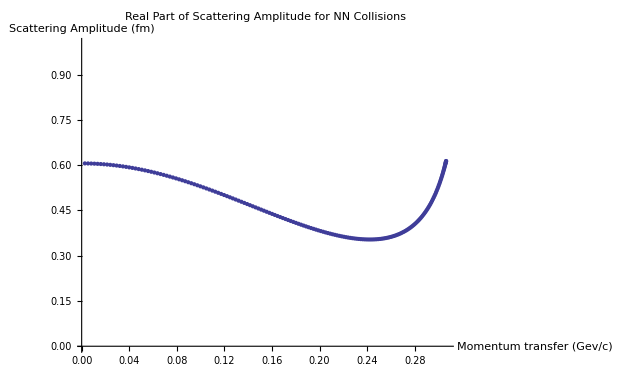

```mathematica
ListPlot[Transpose[{NN50[[All,1]],Re[NN50[[All,2]]]}],PlotLabel->"Real Part of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,1}]
```

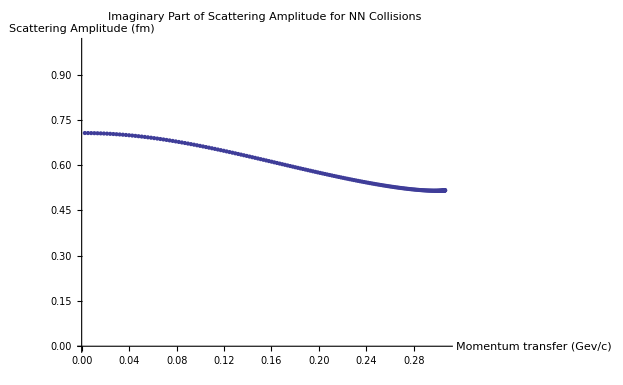

```mathematica
ListPlot[Transpose[{NN50[[All,1]],Im[NN50[[All,2]]]}],PlotLabel->"Imaginary Part of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,1}]
```

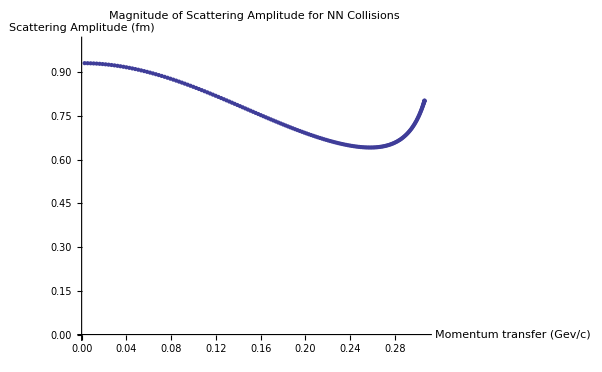

```mathematica
ListPlot[Transpose[{NN50[[All,1]],Abs[NN50[[All,2]]]}],PlotLabel->"Magnitude of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,1}]
```

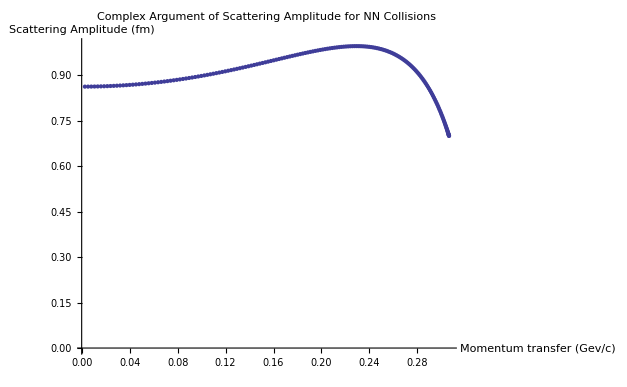

```mathematica
ListPlot[Transpose[{NN50[[All,1]],Arg[NN50[[All,2]]]}],PlotLabel->"Complex Argument of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,1}]
```

## Fit data to complex gaussian (see model on next line)

```mathematica
Clear[β,ρ,σ]
model=κ σ (I+ρ)/(4 Pi) Exp[-β q^2];
```

The fit is only performed over the first 50 degrees.

{a→0.929778,βre→8.92709}

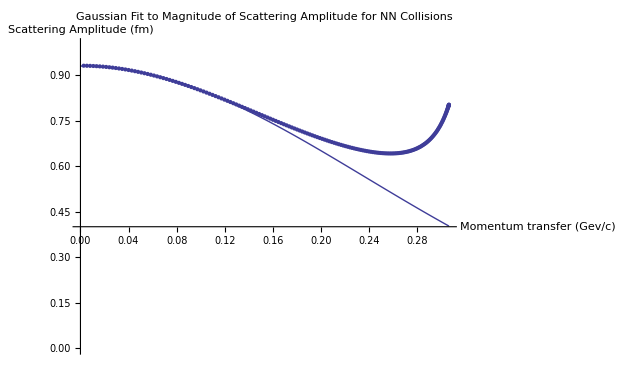

```mathematica
Npts=50;
FindFit[Transpose[{NN50[[1;;Npts,1]],Abs[NN50[[1;;Npts,2]]]}],a Exp[-βre q^2],{a,βre},q]
Show[Plot[a Exp[-βre q^2]/.%,{q,0,2 κ}],ListPlot[Transpose[{NN50[[All,1]],Abs[NN50[[All,2]]]}]],PlotLabel->"Gaussian Fit to Magnitude of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,1}]
```

{ρ→0.857387,βim→-3.5168}

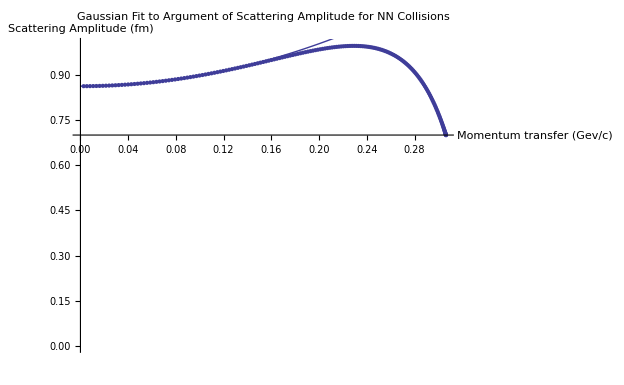

```mathematica
FindFit[Transpose[{NN50[[1;;Npts,1]],Arg[NN50[[1;;Npts,2]]]}],ArcTan[ρ,1]-βim q^2,{ρ,βim},q]
Show[ListPlot[Transpose[{NN50[[All,1]],Arg[NN50[[All,2]]]}]],Plot[ArcTan[ρ,1]-βim q^2/.%,{q,0,2 κ}],PlotLabel->"Gaussian Fit to Argument of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,1}]
```

```mathematica
NSolve[κ/ℏc σ Sqrt[1+ρ^2]/(4 Pi)==0.9297784002346322&&ρ==0.8573867189981697,{σ,ρ}]
```

{{σ→11.4243,ρ→0.857387}}

Fitted parameters:

```mathematica
σ=11.424258898051162;
ρ=0.8573867189981697;
β=8.9270917212192-3.516797972227385 I;
```

## Glauber

```mathematica
σ1=-σ/ℏc^2 (1-I ρ)/(8 Pi β)
Fcm[q_]:=Exp[B*q^2/A]
```

-1.51436+0.524619 ⅈ

```mathematica
F0[q_]:=-2*I*k*Fcm[q]*(B+β)*Sum[Binomial[A,j]/j*(-σ (1-I ρ)/ℏc^2/(8 Pi (B+β)))^j*Exp[-(B+β)*q^2/j],{j,1,A}]*ℏc
```

Glauber aNNroximation  for p-α scattering is below:

```mathematica
40*Pi/(k/ℏc) Im[F0[0]]
```

340.804

## Add in First Order Correction

```mathematica
Γ[b_]:=σ1 Exp[-b^2/(4 β)]
```

```mathematica
Γ[0]
```

-1.51436+0.524619 ⅈ

```mathematica
Clear[U]
```

```mathematica
Utemp[q_]:=2*Pi*I*NIntegrate[b*BesselJ[0,b*q]*Log[1-Γ[b]],{b,0,Infinity}]
```

```mathematica
U=Quiet[Interpolation[Table[{q,Utemp[q]},{q,0,2 κ,.01}]]];
```

```mathematica
U[0]
```

87.5521+117.791 ⅈ

Wallace parameterizes it as a gaussian in q, so we should check the validity of that assertion:

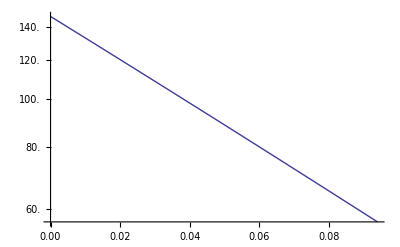

```mathematica
Quiet[LogPlot[Abs[U[Sqrt[q]]],{q,0,(2 κ)^2}]]
```

The magnitude seems to be well approximated by a gaussian.

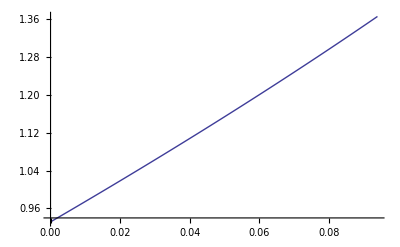

```mathematica
Quiet[Plot[Arg[U[Sqrt[q]]],{q,0,(2 κ)^2}]]
```

```mathematica
γ=100*Quiet[(Log[U[0]]-Log[U[0.1]])]
```

10.0302-4.3176 ⅈ

```mathematica
Z=U[0]/(-I*4*Pi*σ1*β)(*Unitless*)
```

0.757674+0.0528023 ⅈ

Here are a bunch of parameters that Wallace has defined in his paper.

```mathematica
γ1:=γ*β/(γ+β)(*(c/GeV)^2*)
αnL[n_,L_]:=If[n==1,(2*(γ+B)^-1+L*(β+B)^-1)^-1,If[n==2,((γ+B)^-1+(γ1+B)^-1+L*(β+B)^-1)^-1,If[n==3,(2*(γ1+B)^-1+L*(β+B)^-1)^-1]]]
an[n_]:=If[n==1,(γ+B)^-2,If[n==2,-2*σ1*(γ1/γ)*(γ+B)^-1*(γ1+B)^-1,If[n==3,σ1^2*(γ1/γ)^2*(γ1+B)^-2]]]
bn[n_]:=If[n==1,(γ+B)^-3,If[n==2,-σ1*(γ1/γ)*(γ1+B)^-1*(γ+B)^-1*((1-B*γ1/(β*(B+γ1)))/(γ+B)+(1-γ1/β)/(γ1+B)),If[n==3,σ1^2*(γ1/γ)^2*(γ1+B)^-3*(1-B*γ1/(β*(B+γ1)))*(1-γ1/β)]]]
γ2:=γ*β/(β+2*γ)(*(c/GeV)^2*)
βnL[n_,L_]:=If[n==1,((γ/2+B)^-1+L*(β+B)^-1)^-1,If[n==2,((γ2/2+B)^-1+L*(β+B)^-1)^-1]]
cn[n_]:=If[n==1,(γ-2*B)*(γ+2*B)^-2,If[n==2,-σ1(γ2/γ1)*(γ2+2*B)^-1*(1-2*γ2/γ+2*(γ2)^2/(γ*(γ2+2*B)))]]
dn[n_]:=If[n==1,γ*(γ+2*B)^-3,If[n==2,
-σ1*(γ)^-2*(γ2/(γ2+2*B))^3]]
```

```mathematica
FO1[q_(*c/GeV*)]:=A*(A-1)*Fcm[q]*ηO*(β*σ1*Z)^2/(2*(2*Pi*(B+β))^(1/2))*Sum[Binomial[A-2,L]*(-σ1*β/(B+β))^L*Sum[αnL[n,L]*(an[n]-4*αnL[n,L]*bn[n]*(1-αnL[n,L]q^2))*Exp[-αnL[n,L]*q^2],{n,1,3}],{L,0,A-2}]*ℏc
```

```mathematica
FD1[q_(*c/GeV*)]:=A*Fcm[q]*ηD*(β*σ1*Z)^2/(2*γ*Sqrt[2*Pi*γ])*Sum[Binomial[A-1,L]*(-σ1*β/(B+β))^L*Sum[βnL[n,L]*(cn[n]-4*βnL[n,L]*dn[n]*(1-βnL[n,L]*q^2))*Exp[-βnL[n,L]*q^2],{n,1,2}],{L,0,A-1}]*ℏc
```

```mathematica
Im[FO1[0]+FD1[0]]/Im[F0[0]]
```

-0.0300873

The first order correction is about 3% at 50 MeV.

```mathematica
40*Pi/(k/ℏc) Im[F0[0]]
40*Pi/(k/ℏc) Im[FO1[0]+FD1[0]]
40*Pi/(k/ℏc) Im[FO1[0]+FD1[0]+F0[0]]
```

340.804

-10.2539

330.55

```mathematica
FO1[0]
```

-0.263966-0.0092183 ⅈ

```mathematica
FD1[0]
```

0.196619-0.0926046 ⅈ

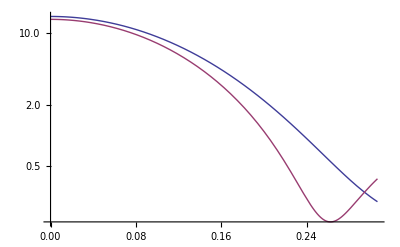

```mathematica
LogPlot[{Abs[F0[q]]^2,Abs[F0[q]+FO1[q]+FD1[q]]^2},{q,0,2 κ}]
```